# Chapter 18

```mathematica
GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]]
```

3453.71 mi

```mathematica
GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]]/GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"SanFrancisco","California","UnitedStates"}]]
```

1.35109

```mathematica
UnitConvert[GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]],Quantity[, "Kilometers"]]
```

5558.2 km

```mathematica
GeoGraphics[Entity["Country","UnitedStates"]]
```

-Graphics-

```mathematica
GeoListPlot[{Entity["Country","Brazil"],Entity["Country","Russia"],Entity["Country","India"],Entity["Country","China"]}]
```

-Graphics-

```mathematica
GeoGraphics[GeoPath[{Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Beijing","Beijing","China"}]}]]
```

GeoServer::vtiles: Unable to download one or more vector tiles.

-Graphics-

```mathematica
GeoGraphics[GeoDisk[GeoPosition[{EntityClass["Building","PyramidsGiza"]}],Quantity[10, "Miles"]]]
```

GeoDisk::cntr: … is not a valid center location.

-Graphics-

```mathematica
GeoGraphics[GeoDisk[Entity["City",{"NewYork","NewYork","UnitedStates"}],GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"SanFrancisco","California","UnitedStates"}]]]]
```

GeoServer::vtiles: Unable to download one or more vector tiles.

-Graphics-

```mathematica
GeoImage[GeoDisk[Entity["Building","ThePentagon::qzh8d"],Quantity[0.4, "Miles"]]]
```

-Graphics-

```mathematica
GeoNearest["Country",GeoPosition["NorthPole"],5]
```

```mathematica
{Entity["Country","Greenland"],Entity["Country","Canada"],Entity["Country","Russia"],Entity["Country","Svalbard"],Entity["Country","UnitedStates"]}
```

{Greenland,Canada,Russia,Svalbard,United States}


{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[GeoNearest["Country",GeoPosition[{45,0}],3],"Flag"]
```

```mathematica
GeoListPlot[GeoNearest["Volcano",Entity["City",{"Rome","Lazio","Italy"}],25]]
```

-Graphics-

```mathematica
GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]][[1,1]]-GeoPosition[Entity["City",{"LosAngeles","California","UnitedStates"}]][[1,1]]
```

6.64488

# Chapter 19

```mathematica
Length[DayRange[DateObject[{1900,1,1},"Day"],Now]]
```

45698

```mathematica
DayName[DateObject[{1900,1,1},"Day"]]
```

Monday

```mathematica
Today-Quantity[100000, "Years"]
```

Tue 11 Feb 97976 BC

```mathematica
LocalTime[Entity["City",{"Delhi","Delhi","India"}]]
```

Tue 11 Feb 2025 20:59:46GMT+5.5

```mathematica
Sunset[Entity["City",{"Minneapolis","Minnesota","UnitedStates"}],Today]-Sunrise[Entity["City",{"Minneapolis","Minnesota","UnitedStates"}],Today]
```

10.2741 h

```mathematica
MoonPhase[Today,"Icon"]
```

-Graphics-

```mathematica
Table[MoonPhase[Today+x Quantity[, "Days"]],{x,0,9,1}]
```

{0.982229,0.998567,0.994059,0.970017,0.928388,0.871492,0.801795,0.721766,0.633831,0.540416}

```mathematica
Table[MoonPhase[Today+x Quantity[, "Days"],"Icon"],{x,0,9,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Sunrise[Entity["City",{"NewYork","NewYork","UnitedStates"}]]-Sunrise[Entity["City",{"London","GreaterLondon","UnitedKingdom"}]]
```

4.55435 h

```mathematica
UnitConvert[Now-DateObject[Entity["MannedSpaceMission","Apollo11"][EntityProperty["MannedSpaceMission","LunarLandingDate"]]],"Years"]
```

55.6022 yr

```mathematica
AirTemperatureData[Entity["City",{"Paris","IleDeFrance","France"}],DateObject[{2025,2,10,12,0,0},"Instant","Gregorian",-7.]]
```

41. °F

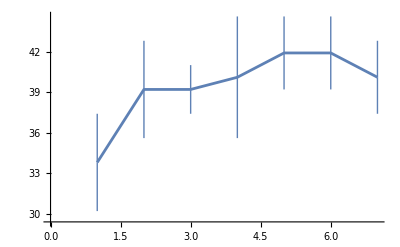

```mathematica
ListLinePlot[Table[AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],DateObject[{2025,2,4},"Day"]+x Quantity[, "Days"]],{x,0,6}]]
```

```mathematica
AirTemperatureData[Entity["City",{"NewYork","NewYork","UnitedStates"}]]-AirTemperatureData[Entity["City",{"LosAngeles","California","UnitedStates"}]]
```

-20.2 _Δ^◦F

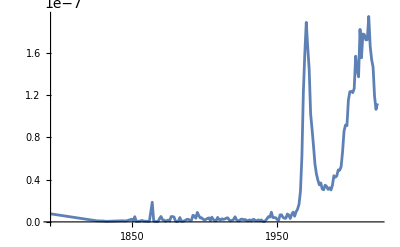

```mathematica
ListLinePlot[WordFrequencyData["groovy","TimeSeries"]]
```

```mathematica
Entity["Country","UnitedKingdom"][Dated["Population",2000]]-Entity["Country","UnitedKingdom"][Dated["Population",1900]]
```

20759628 people